# Laboratorium #1 Jakub Zbrzezny, nr indeksu: 286689

## Zadanie 1 (a)

Przyjmujemy, że c = C.

```mathematica
equation = x^3 y[x] - c y[x]^2 == c;
```

```mathematica
step1 = Dt[equation,x, Constants -> {c}]
```

3 x^2 y[x]+x^3 y'[x]-2 c y[x] y'[x]==0

Różniczkując równość z zadania po x otrzymaliśmy równanie różniczkowe zwyczajne 1-go rzędu. Oznaczmy je (*).

Teraz narysujemy krzywe  dla kilku wartości stałej c.

1. c = 0.

```mathematica
sol = DSolve[3 x^2 y[x]+x^3 y'[x]== 0, y[x], x]
```

{{y[x]→C[1]/x^3}}

```mathematica
solutions = Table[Evaluate[y[x]]/.sol/.C[1]->i,{i,0,5}];
```

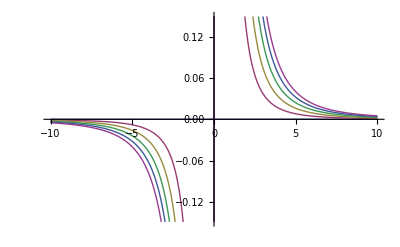

```mathematica
Plot[solutions, {x, -10, 10}]
```

2. c = -1.

```mathematica
sol=DSolve[3 x^2 y[x] + x^3 y'[x] + 2 y[x] y'[x] == 0, y[x], x]
```

{{y[x]→-x^3/2-(√(x^6/2+2 C[1]))/(√2)},{y[x]→-x^3/2+(√(x^6/2+2 C[1]))/(√2)}}

```mathematica
solutions = Table[Evaluate[y[x]]/.sol/.C[1]->i,{i,0,5}];
```

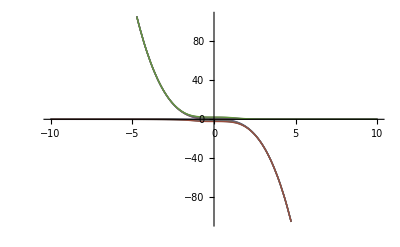

```mathematica
Plot[solutions, {x, -10, 10}]
```

3. c = 1.

```mathematica
sol = DSolve[3 x^2 y[x] + x^3 y'[x] - 2 y[x] y'[x] == 0, y[x], x]
```

{{y[x]→x^3/2-(ⅈ √(-x^6/2-2 C[1]))/(√2)},{y[x]→x^3/2+(ⅈ √(-x^6/2-2 C[1]))/(√2)}}

```mathematica
solutions = Table[Evaluate[y[x]]/.sol/.C[1]->i, {i, 0, 5}];
```

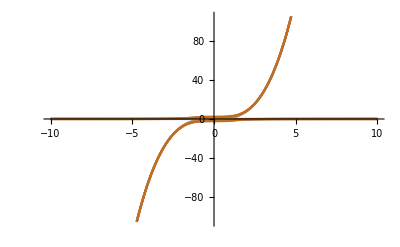

```mathematica
Plot[solutions, {x, -10, 10}]
```

4. c = 5.

```mathematica
sol = DSolve[3 x^2 y[x] + x^3 y'[x] - 10  y[x] y'[x] == 0, y[x], x]
```

{{y[x]→x^3/10-(ⅈ √(-x^6/10-10 C[1]))/(√10)},{y[x]→x^3/10+(ⅈ √(-x^6/10-10 C[1]))/(√10)}}

```mathematica
solutions = Table[Evaluate[y[x]]/.sol/.C[1]->i, {i, 0, 5}];
```

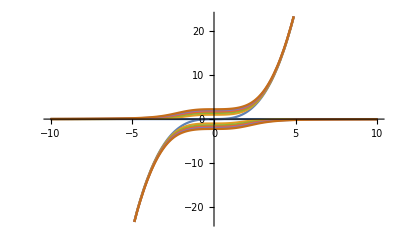

```mathematica
Plot[solutions, {x, -10, 10}]
```

Musimy pozbyć się parametru C z otrzymanego równania (*). 
Wyznaczamy C z równania, z treści zadania.
Zauważmy, że C(1 + (y[x])^2) = x^3 y[x]. 1 + (y[x])^2> 0, zatem możemy podzielić obustronnie równanie przez 1 + (y[x])^2.
Stąd C = (x^3 y[x])/(1 + (y[x])^2).

```mathematica
c = (x^3 y[x])/(1 + (y[x])^2)
```

(x^3 y[x])/(1+y[x]^2)

```mathematica
3 x^2 y[x]+x^3 y'[x]-2 c y[x] y'[x]
```

3 x^2 y[x]+x^3 y'[x]-(2 x^3 y[x]^2 y'[x])/(1+y[x]^2)

Czyli po wstawieniu C do równania (*) otrzymaliśmy równanie:
3 x^2 y[x]+x^3 y'[x]-(2 x^3 y[x]^2 y'[x])/(1+y[x]^2) = 0.

Jeśli chodzi o jednoznaczność rozwiązania równania (*) dla dowolnego warunku początkowego, to nie jest prawdą, że rozwiązanie równania (*) dla dowolnego warunku początkowego jest jednoznaczne, ponieważ dla warunku początkowego y[1] = 1:

```mathematica
DSolve[{3 x^2 y[x]+x^3 y'[x]-(2 x^3 y[x]^2 y'[x])/(1+y[x]^2) ==0,  y[1] ==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→x^3-√(-1+x^6)},{y[x]→x^3+√(-1+x^6)}}

Różne funkcje y1(x) = x^3-√(-1+x^6), y2(x)=x^3+√(-1+x^6) są rozwiązaniami równania (*).

## Zadanie 2 (b)

x x’  + t  = 0  <=>  x’ = - t/x
f(t, x) = - t/x
f(t, x) jest portretem fazowym równania z treści zadania.
x’(t) = f(t, x)

```mathematica
f[t_, x_] := -t/x;
```

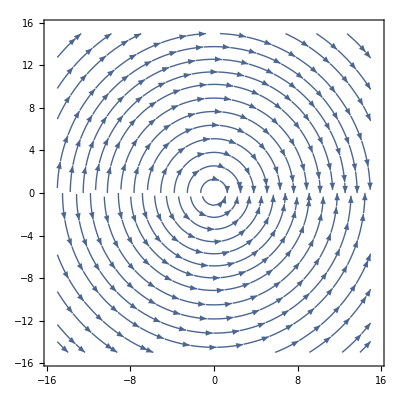

```mathematica
strpl = StreamPlot[{1, f[t, x]}, {t, -15, 15}, {x, -15, 15}]
```

Rozwiązujemy zagadnienia z następującymi warunkami początkowymi:
a) x(0) = -10
b) x(0) = 1
c) x(0) = 10

a)

```mathematica
sol1 = DSolve[{x'[t] == f[t, x[t]],  x[0] ==-10},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{x[t]→-√(100-t^2)}}

```mathematica
solutions1=Table[Evaluate[x[t]/.sol1/.C[1]-> i],{i,-2,1,0.5}];
```

b)

```mathematica
sol2 = DSolve[{x'[t] == f[t, x[t]],  x[0] ==1},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{x[t]→√(1-t^2)}}

```mathematica
solutions2=Table[Evaluate[x[t]/.sol2/.C[1]-> i],{i,-2,1,0.5}];
```

c)

```mathematica
sol3 = DSolve[{x'[t] == f[t, x[t]],  x[0] ==10},x[t],t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{x[t]→√(100-t^2)}}

```mathematica
solutions3=Table[Evaluate[x[t]/.sol3/.C[1]-> i],{i,-2,1,0.5}];
```

Teraz nanosimy otrzymane rozwiązania na wykres vectpl.
Portret fazowy ma kolor niebieski.
Wykres rozwiązania zagadnienia z warunkiem początkowym x(0) = -10 jest oznaczony kolorem pomarańczowym.
Wykres rozwiązania zagadnienia z warunkiem początkowym x(0)=1  jest oznaczony kolorem zielonym.
Wykres rozwiązania zagadnienia z warunkiem początkowym x(0)=10 jest oznaczony kolorem fioletowym.

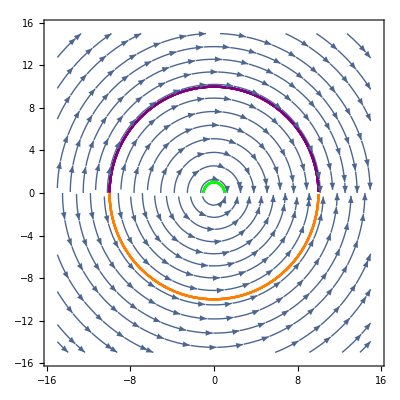

```mathematica
Show[strpl,
Plot[solutions1,{t,-15,15},PlotRange->{{-15,15},{-15,15}}, PlotStyle->Orange],
Plot[solutions2,{t,-15,15},PlotRange->{{-15,15},{-15,15}}, PlotStyle->Green],
Plot[solutions3,{t,-15,15},PlotRange->{{-15,15},{-15,15}},PlotStyle->Purple]]
```

## Zadanie 3 (a)

Mamy równanie (3 t^2 + y^2) dt + (2 t y + 1) dy = 0. Oznaczmy je (*)
P(t, y) = 3 t^2 + y^2
Q(t, y) = 2 t y + 1
Równanie (*) jest zupełnie wtedy i tylko wtedy, gdy P_y = Q_t.

```mathematica
p[t_, y_] := 3 t^2 + y^2;
```

```mathematica
q[t_, y_] := 2 t y + 1;
```

Sprawdzamy zupełność równania (*).

```mathematica
D[p[t,y],y]-D[q[t,y],t]==0
```

True

Czyli P_y = Q_t, zatem równanie (*) jest zupełne.
Stąd istnieje potencjał f(t, y) taki, że grad(f) = (P, Q).

Wyznaczymy potencjał f(t, y).

```mathematica
step1 = Integrate[p[t, y], t]
```

t^3+t y^2

```mathematica
step2 = D[step1+c[y],y]
```

2 t y+c'[y]

```mathematica
step3=DSolve[step2==q[t,y],c[y],y]
```

{{c[y]→y+C[1]}}

```mathematica
f[t_, y_]:= step1
```

```mathematica
f[t,y]
```

t^3+t y^2

Czyli funkcja potencjału f(t, y) wynosi t^3+ t y^2.

Teraz narysujemy pole wektorowe związane z równaniem (*) i naniesiemy kilka krzywych całkowych tego równania.
Mamy: f(t, y) = c, c - stała rzeczywista.
Czyli: t^3 + t y^2= c.
 
 1. Dla c = 1.
 t^3 + t y^2 = 1

```mathematica
equation1 = t^3 + t y[t]^2 == 1;
```

```mathematica
step1 = Dt[equation1, t]
```

3 t^2+y[t]^2+2 t y[t] y'[t]==0

```mathematica
sol1=DSolve[{3 t^2+y[t]^2+2 t y[t] y'[t]==0, y[1] == 0},y[t],t]
```

{{y[t]→-(√(1-t^3))/(√t)},{y[t]→(√(1-t^3))/(√t)}}

```mathematica
solutions1=Table[Evaluate[y[t]]/.sol1/.C[1]->i,{i,-5,5}];
```

2. Dla c = -1.
 t^3 + t y^2 = -1

```mathematica
equation2 = t^3 + t y[t]^2 == -1;
```

```mathematica
step1 = Dt[equation2, t]
```

3 t^2+y[t]^2+2 t y[t] y'[t]==0

```mathematica
sol2=DSolve[{3 t^2+y[t]^2+2 t y[t] y'[t]==0, y[-1] == 0},y[t],t]
```

{{y[t]→-(√(-1-t^3))/(√t)},{y[t]→(√(-1-t^3))/(√t)}}

```mathematica
solutions2=Table[Evaluate[y[t]]/.sol2/.C[1]->i,{i,-5,5}];
```

3. Dla c =5.
 t^3 + t y^2 = 5

```mathematica
equation3 = t^3 + t y[t]^2 == 5;
```

```mathematica
step1 = Dt[equation3, t]
```

3 t^2+y[t]^2+2 t y[t] y'[t]==0

```mathematica
sol3=DSolve[{3 t^2+y[t]^2+2 t y[t] y'[t]==0, y[1]^2 == 4},y[t],t]
```

{{y[t]→-(√(5-t^3))/(√t)},{y[t]→(√(5-t^3))/(√t)}}

```mathematica
solutions3=Table[Evaluate[y[t]]/.sol3/.C[1]->i,{i,-5,5}];
```

4. Dla c = -5.
 t^3 + t y^2 = -5

```mathematica
equation4 = t^3 + t y[t]^2 == -5;
```

```mathematica
step1 = Dt[equation4, t]
```

3 t^2+y[t]^2+2 t y[t] y'[t]==0

```mathematica
sol4=DSolve[{3 t^2+y[t]^2+2 t y[t] y'[t]==0, y[-1]^2 == 4},y[t],t]
```

{{y[t]→-(√(-5-t^3))/(√t)},{y[t]→(√(-5-t^3))/(√t)}}

```mathematica
solutions4=Table[Evaluate[y[t]]/.sol4/.C[1]->i,{i,-5,5}];
```

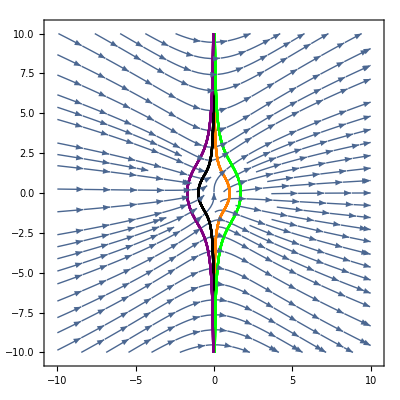

```mathematica
Show[StreamPlot[{p[t,y], q[t, y]}, {t, -10, 10}, {y, -10, 10}],
Plot[solutions1,{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Orange],
Plot[solutions2,{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Black],
Plot[solutions3,{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Green],
Plot[solutions4,{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Purple]]
```

Wykres pola wektorowego ma kolor niebieski.
Krzywa całkowa równania (*) dla c = 1 ma kolor pomarańczowy.
Krzywa całkowa równania (*) dla c = -1 ma kolor czarny.
Krzywa całkowa równania (*) dla c = 5 ma kolor zielony.
Krzywa całkowa równania (*) dla c = -5 ma kolor fioletowy.

## Zadanie 4 (b)

Mamy równanie x’’−6 x’ +9 x = 9 t^2 −12 t + 2. Oznaczmy je (*).

```mathematica
sol=DSolve[x''[t]−6 x'[t]+9 x[t]==9 t^2−12 t+2, x[t], t]
```

{{x[t]→t^2+ⅇ^(3 t) C[1]+ⅇ^(3 t) t C[2]}}

W ten sposób otrzymaliśmy rozwiązanie ogólne równania drugiego rzędu (*). 
Jest ono równe x(t) = t^2 + e^(3 t) c[1] + e^(3 t) t C[2]. 

Otrzymany wynik jest warstwą dwuwymiarowej przestrzeni liniowej V rozpiętej na dwóch wektorach bazowych, ponieważ:
Biorąc y(t) = (x(t), (x'(t)))^T mamy równanie:
d/dty(t) ={{0, 1}, {6, -9}} y(t) + (0, 9 t^2 - 12 t + (2))^T. (#)
Zauważmy, że jest to równanie liniowe.
y należy do przestrzeni dwuwymiarowej. Z teorii równań różniczkowych zwyczajnych wiemy, że zbiór rozwiązań zbiór rozwiązań równania d/dty(t) ={{0, 1}, {6, -9}} y(t) ma strukturę przestrzeni liniowej. Ponadto jest wymiaru 2, wynika to z następującego twierdzenia:
y_1(t), ..., y_k(t) - rozwiązania równania (#)
{y_1(t), ..., y_k(t)} jest układem fundamentalnym wtedy i tylko wtedy, gdy  k = 2 i {y_1(t), ...., y_k(t)} jest liniowo niezależny.

Def.: Układem fundamentalnym nazywamy bazę w zbiorze rozwiązań wysyconych równania jednorodnego.

Ponadto mamy, że zbiór postaci x_s(t) + V jest warstwą V, gdzie x_s(t) jest rozwiązaniem szczególnym.


Teraz narysujemy na wykresie rozwiązania równania (*) dla różnych wartości C1 i C2 = 0.

1. C1 = 0
x(t) = t^2

```mathematica
x1[t_]:=t^2;
```

2. C1 = 1.
x(t) = t^2 + e^(3 t)

```mathematica
x2[t_]:=t^2+Exp[3 t];
```

3. C1 = -5.
x(t) = t^2-5 e^(3 t)

```mathematica
x3[t_]:=t^2-5 Exp[3 t];
```

4. C1 = 10.
x(t) = t^2 + 10 e^(3 t)

```mathematica
x4[t_]:=t^2 + 10 Exp[3 t];
```

Dla C1 = 0 wykres rozwiązania równania (*) ma kolor zielony.
Dla C1 = 1 wykres rozwiązania równania (*) ma kolor czarny.
Dla C1 = -5 wykres rozwiązania równania (*) ma kolor pomarańczowy.
Dla C1 = 10 wykres rozwiązania równania (*) ma kolor fioletowy.

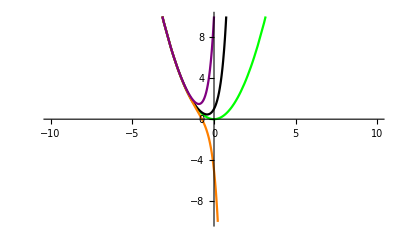

```mathematica
Show[Plot[x1[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Green],
Plot[x2[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Black],
Plot[x3[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Orange],
Plot[x4[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Purple]]
```

Narysujemy na wykresie rozwiązania równania (*) dla różnych wartości C2 i C1 = 0.

1. C2 = 0.
x(t) = t^2

```mathematica
x1[t_]:= t^2;
```

2. C2 = 1.
x(t) = t^2 + t e^(3 t)

```mathematica
x2[t_]:=t^2 + t Exp[3 t];
```

3. C2 = -5.
x(t) = t^2 - 5 t e^(3 t)

```mathematica
x3[t_]:=t^2 - 5 t Exp[3 t];
```

4. C2 = 10.
x(t) = t^2 + 10 t e^(3 t)

```mathematica
x4[t_]:=t^2 + 10 t Exp[3 t];
```

Dla C2 = 0 wykres rozwiązania równania (*) ma kolor zielony.
Dla C2 = 1 wykres rozwiązania równania (*) ma kolor czarny.
Dla C2 = -5 wykres rozwiązania równania (*) ma kolor pomarańczowy.
Dla C2 = 10 wykres rozwiązania równania (*) ma kolor fioletowy.

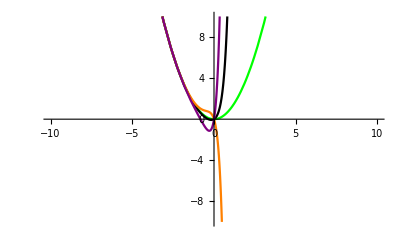

```mathematica
Show[Plot[x1[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Green],
Plot[x2[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Black],
Plot[x3[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Orange],
Plot[x4[t],{t,-10,10},PlotRange->{{-10,10},{-10,10}}, PlotStyle->Purple]]
```

## Zadanie dodatkowe.

(a)

Mamy równanie: (2 t +1) x’’ + 2 (2 t − 1) x’ − 8 x = 0. Oznaczmy je (*).

```mathematica
Constants->{m};
```

```mathematica
x[t_]:= Exp[m t];
```

```mathematica
(2 t + 1) x''[t] + 2 (2 t - 1) x'[t] - 8 x[t]
```

-8 ⅇ^(m t)+2 ⅇ^(m t) m (-1+2 t)+ⅇ^(m t) m^2 (1+2 t)

```mathematica
equation = -8 ⅇ^(m t)+2 ⅇ^(m t) m (-1+2 t)+ⅇ^(m t) m^2 (1+2 t)==0;
```

```mathematica
Simplify[equation]
```

ⅇ^(m t) (2+m) (-4+m+2 m t)==0

Funkcja e^(m t) jest rozwiązaniem równania (*) wtedy i tylko wtedy, gdy ⅇ^(m t) (2+m) (-4+m+2 m t)= 0 dla każdego t należącego do zbioru liczb rzeczywistych.

```mathematica
Solve[ⅇ^(m t) (2+m) (-4+m+2 m t)==0, m]
```

{{m→-2},{m→4/(1+2 t)}}

Zatem jedyną stałą m taką, że e^(m t) jest rozwiązaniem równania (*) jest m = -2.
Drugiego rozwiązania szukamy w postaci v(t) = a(t) e^(-2 t), gdzie a nie jest stała. 
Wstawiając do równania otrzymujemy:

```mathematica
v[t_] := a[t] Exp[-2 t];
```

```mathematica
(2 t + 1) v''[t] + 2 (2 t - 1)v'[t] - 8v[t]
```

-8 ⅇ^(-2 t) a[t]+2 (-1+2 t) (-2 ⅇ^(-2 t) a[t]+ⅇ^(-2 t) a'[t])+(1+2 t) (4 ⅇ^(-2 t) a[t]-4 ⅇ^(-2 t) a'[t]+ⅇ^(-2 t) a''[t])

Mamy równanie: -8 ⅇ^(-2 t) a[t]+2 (-1+2 t) (-2 ⅇ^(-2 t) a[t]+ⅇ^(-2 t) a'[t])+(1+2 t) (4 ⅇ^(-2 t) a[t]-4 ⅇ^(-2 t) a'[t]+ⅇ^(-2 t) a''[t]) = 0.

```mathematica
DSolve[-8 ⅇ^(-2 t) a[t]+2 (-1+2 t) (-2 ⅇ^(-2 t) a[t]+ⅇ^(-2 t) a'[t])+(1+2 t) (4 ⅇ^(-2 t) a[t]-4 ⅇ^(-2 t) a'[t]+ⅇ^(-2 t) a''[t])==0, a[t], t]
```

{{a[t]→1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2]}}

```mathematica
v[t_] :=( 1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2]) Exp[- 2 t]
```

```mathematica
v[t]
```

ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2])

Czyki v[t] = ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2]) jest drugim rozwiązaniem równania (*)
Zatem wszystkie rozwiązania równania (*) są postaci x(t) = C1  e^(- 2 t) + C2  ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2]) , gdzie C1, C2 są stałymi rzeczywistymi.

(b)

Mamy równanie: t^2 x’’ − 3 t x’ + 4 x = 0. Oznaczmy je (*).

```mathematica
x[t_]:= t^m;
```

```mathematica
Constants->{m}
```

Constants→{m}

```mathematica
t^2 x''[t] - 3 t x'[t] + 4 x[t]
```

4 t^m-3 m t^m+(-1+m) m t^m

```mathematica
equation = 4 t^m-3 m t^m+(-1+m) m t^m == 0;
```

```mathematica
Simplify[equation]
```

(-2+m) t^m==0

Funkcja t^m jest rozwiązaniem równania (*) wtedy i tylko wtedy, gdy (- 2 + m) t^m = 0 dla każdego t należącego do zbioru liczb rzeczywistych.

```mathematica
Solve[(-2+m) t^m==0, m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→2}}

Zatem t^m jest rozwiązaniem równania (*) dla m = 2.
Drugiego rozwiązania szukamy w postaci v(t) = a(t) t^2, gdzie a nie jest stała. 
Wstawiając do równania otrzymujemy:

```mathematica
v[t_] := a[t] t^2;
```

```mathematica
t^2 v''[t] - 3 t v'[t] + 4 v[t]
```

4 ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2])-3 t (2 t a[t]+t^2 a'[t])+t^2 (2 a[t]+4 t a'[t]+t^2 a''[t])

Mamy równanie 4 ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2])-3 t (2 t a[t]+t^2 a'[t])+t^2 (2 a[t]+4 t a'[t]+t^2 a''[t])= 0.

```mathematica
DSolve[4 ⅇ^(-2 t) (1/2 ⅇ^(2 t) (1+4 t^2) C[1]+C[2])-3 t (2 t a[t]+t^2 a'[t])+t^2 (2 a[t]+4 t a'[t]+t^2 a''[t]) == 0, a[t], t]
```

{{a[t]→C[3] Cosh[2 Log[t]]+ⅈ C[4] Sinh[2 Log[t]]+1/(24 t^4)ⅇ^(-2 t) (3 ⅇ^(2 t) C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^6 C[1] Cosh[2 Log[t]]+6 C[2] Cosh[2 Log[t]]-4 t C[2] Cosh[2 Log[t]]+4 t^2 C[2] Cosh[2 Log[t]]-8 t^3 C[2] Cosh[2 Log[t]]+8 ⅇ^(2 t) t^4 C[2] Cosh[2 Log[t]] ExpIntegralEi[-2 t]+12 ⅇ^(2 t) t^4 C[1] Cosh[2 Log[t]] Log[t]+3 ⅇ^(2 t) C[1] Sinh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Sinh[2 Log[t]]-24 ⅇ^(2 t) t^6 C[1] Sinh[2 Log[t]]+6 C[2] Sinh[2 Log[t]]-4 t C[2] Sinh[2 Log[t]]+4 t^2 C[2] Sinh[2 Log[t]]-8 t^3 C[2] Sinh[2 Log[t]]-40 ⅇ^(2 t) t^4 C[2] ExpIntegralEi[-2 t] Sinh[2 Log[t]]-12 ⅇ^(2 t) t^4 C[1] Log[t] Sinh[2 Log[t]])}}

```mathematica
a[t_] := C[3] Cosh[2 Log[t]]+ⅈ C[4] Sinh[2 Log[t]]+1/(24 t^4)ⅇ^(-2 t) (3 ⅇ^(2 t) C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^6 C[1] Cosh[2 Log[t]]+6 C[2] Cosh[2 Log[t]]-4 t C[2] Cosh[2 Log[t]]+4 t^2 C[2] Cosh[2 Log[t]]-8 t^3 C[2] Cosh[2 Log[t]]+8 ⅇ^(2 t) t^4 C[2] Cosh[2 Log[t]] ExpIntegralEi[-2 t]+12 ⅇ^(2 t) t^4 C[1] Cosh[2 Log[t]] Log[t]+3 ⅇ^(2 t) C[1] Sinh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Sinh[2 Log[t]]-24 ⅇ^(2 t) t^6 C[1] Sinh[2 Log[t]]+6 C[2] Sinh[2 Log[t]]-4 t C[2] Sinh[2 Log[t]]+4 t^2 C[2] Sinh[2 Log[t]]-8 t^3 C[2] Sinh[2 Log[t]]-40 ⅇ^(2 t) t^4 C[2] ExpIntegralEi[-2 t] Sinh[2 Log[t]]-12 ⅇ^(2 t) t^4 C[1] Log[t] Sinh[2 Log[t]]);
```

```mathematica
v[t] = a[t] t^2
```

t^2 (C[3] Cosh[2 Log[t]]+ⅈ C[4] Sinh[2 Log[t]]+1/(24 t^4)ⅇ^(-2 t) (3 ⅇ^(2 t) C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^6 C[1] Cosh[2 Log[t]]+6 C[2] Cosh[2 Log[t]]-4 t C[2] Cosh[2 Log[t]]+4 t^2 C[2] Cosh[2 Log[t]]-8 t^3 C[2] Cosh[2 Log[t]]+8 ⅇ^(2 t) t^4 C[2] Cosh[2 Log[t]] ExpIntegralEi[-2 t]+12 ⅇ^(2 t) t^4 C[1] Cosh[2 Log[t]] Log[t]+3 ⅇ^(2 t) C[1] Sinh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Sinh[2 Log[t]]-24 ⅇ^(2 t) t^6 C[1] Sinh[2 Log[t]]+6 C[2] Sinh[2 Log[t]]-4 t C[2] Sinh[2 Log[t]]+4 t^2 C[2] Sinh[2 Log[t]]-8 t^3 C[2] Sinh[2 Log[t]]-40 ⅇ^(2 t) t^4 C[2] ExpIntegralEi[-2 t] Sinh[2 Log[t]]-12 ⅇ^(2 t) t^4 C[1] Log[t] Sinh[2 Log[t]]))

Czyli v[t] = t^2 (C[3] Cosh[2 Log[t]]+ⅈ C[4] Sinh[2 Log[t]]+1/(24 t^4)ⅇ^(-2 t) (3 ⅇ^(2 t) C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^6 C[1] Cosh[2 Log[t]]+6 C[2] Cosh[2 Log[t]]-4 t C[2] Cosh[2 Log[t]]+4 t^2 C[2] Cosh[2 Log[t]]-8 t^3 C[2] Cosh[2 Log[t]]+8 ⅇ^(2 t) t^4 C[2] Cosh[2 Log[t]] ExpIntegralEi[-2 t]+12 ⅇ^(2 t) t^4 C[1] Cosh[2 Log[t]] Log[t]+3 ⅇ^(2 t) C[1] Sinh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Sinh[2 Log[t]]-24 ⅇ^(2 t) t^6 C[1] Sinh[2 Log[t]]+6 C[2] Sinh[2 Log[t]]-4 t C[2] Sinh[2 Log[t]]+4 t^2 C[2] Sinh[2 Log[t]]-8 t^3 C[2] Sinh[2 Log[t]]-40 ⅇ^(2 t) t^4 C[2] ExpIntegralEi[-2 t] Sinh[2 Log[t]]-12 ⅇ^(2 t) t^4 C[1] Log[t] Sinh[2 Log[t]])) jest drugim rozwiązaniem równania (*).

Zatem wszystkie rozwiązania równania (*) są postaci x(t) = C1  t^2 + C2  t^2 (C[3] Cosh[2 Log[t]]+ⅈ C[4] Sinh[2 Log[t]]+1/(24 t^4)ⅇ^(-2 t) (3 ⅇ^(2 t) C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Cosh[2 Log[t]]+24 ⅇ^(2 t) t^6 C[1] Cosh[2 Log[t]]+6 C[2] Cosh[2 Log[t]]-4 t C[2] Cosh[2 Log[t]]+4 t^2 C[2] Cosh[2 Log[t]]-8 t^3 C[2] Cosh[2 Log[t]]+8 ⅇ^(2 t) t^4 C[2] Cosh[2 Log[t]] ExpIntegralEi[-2 t]+12 ⅇ^(2 t) t^4 C[1] Cosh[2 Log[t]] Log[t]+3 ⅇ^(2 t) C[1] Sinh[2 Log[t]]+24 ⅇ^(2 t) t^2 C[1] Sinh[2 Log[t]]-24 ⅇ^(2 t) t^6 C[1] Sinh[2 Log[t]]+6 C[2] Sinh[2 Log[t]]-4 t C[2] Sinh[2 Log[t]]+4 t^2 C[2] Sinh[2 Log[t]]-8 t^3 C[2] Sinh[2 Log[t]]-40 ⅇ^(2 t) t^4 C[2] ExpIntegralEi[-2 t] Sinh[2 Log[t]]-12 ⅇ^(2 t) t^4 C[1] Log[t] Sinh[2 Log[t]])) , gdzie C1, C2 są stałymi rzeczywistymi.